# GEV Idea Test

## Rebuild and Test of TRS GEV Pencil

```mathematica
m=12
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
g=RandomReal[{-1,1},m];
B=RandomReal[{-1,1},{m,m}];B=B.Bᵀ;
Δ=0.2;
M0 = ArrayFlatten[({{-B, A}, {A, -KroneckerProduct[g,g]/Δ^2}})];
M1=ArrayFlatten[({{0, B}, {B, 0}})];
{λs,vs} =Sort[Chop[Eigensystem[{M0,M1}]]ᵀ]ᵀ;
{y1,y2}=Partition[vs⟦1⟧,m];
pMinGEV=-Sign[g.y2] Δ y1/(√(y1.B.y1));
f[p_]:= 0.5 p.A.p + g.p
Cons[p_]:=p.B.p-Δ^2 
vars=Array[x,m];
vars0=RandomReal[{-1,1},m];
{FMVal,FMinSub}=FindMinimum[{0.5 vars.A.vars + g.vars,vars.B.vars<=Δ^2},{vars, vars0}ᵀ,PrecisionGoal->10] ;
pMinFM=vars/.FMinSub;
TableForm[{{FullForm[f[p]],Cons[p]}/.p->pMinGEV,
{FullForm[f[p]],Cons[p]}/.p->pMinFM},
TableHeadings->{{"GEV","FindMin"},{"obj","cons: p.B.p-Δ^2"}}]
```

12

| obj | cons: p.B.p-Δ^2
GEV | -1.11038 | 1.80411×10^-15
FindMin | -1.11038 | 9.99948×10^-9

Making functions.

```mathematica
TRSMatrices[A_,B_,g_,Δ_]:= Module[{},
(* M0 and M1 *)
Map[ ArrayFlatten,{({{-B, A}, {A, -KroneckerProduct[g,g]/Δ^2}}),({{0, B}, {B, 0}})}]
]
TRSMin[A_,B_,g_,Δ_]:= Module[{m=Length[A],M0,M1, λs,vs,y1,y2},
{M0,M1}=TRSMatrices[A,B,g,Δ];
(* Does not treat or test the hard case *)
{λs,vs} =Sort[Chop[Eigensystem[{M0,M1}]]ᵀ]ᵀ;
{y1,y2}=Partition[vs⟦1⟧,m];
(* This is the constrained argmin *)
-Sign[g.y2] Δ y1/(√(y1.B.y1))
]
```

Testing the function

```mathematica
{m,Δ}={12,0.2};
{A,B}=RandomReal[{-1,1},{2,m,m}];{A,B}={A+Aᵀ,B.Bᵀ};
g=RandomReal[{-1,1},m];
pMinGEV=TRSMin[A,B,g,Δ];
Clear[f,Cons,x,p]
f[p_]:= 0.5 p.A.p + g.p
Cons[p_]:=p.B.p-Δ^2 
{vars,vars0}={Array[x,m],RandomReal[{-1,1},m]};
{FMVal,FMinSub}=FindMinimum[{0.5 vars.A.vars + g.vars,vars.B.vars<=Δ^2},{vars, vars0}ᵀ] ;
pMinFM=vars/.FMinSub;
TableForm[{{FullForm[f[p]],Cons[p]}/.p->pMinGEV,
{FullForm[f[p]],Cons[p]}/.p->pMinFM},
TableHeadings->{{"GEV","FindMin"},{"obj","cons: p.B.p-Δ^2"}}]
```

| obj | cons: p.B.p-Δ^2
GEV | -1.10371 | -2.08167×10^-16
FindMin | -1.10371 | 4.81695×10^-9

## KKT Matrix with Equality Constraints

```mathematica
{m,c}={13,3};
{A,G}=Map[RandomReal[{-1,1},{#,m}]&,{m,c}]; A=A+Aᵀ;
g=RandomReal[{-1,1},m];
KKT=ArrayFlatten[({{A, Gᵀ}, {G, 0}})];
pμ=LinearSolve[KKT,Join[g,ConstantArray[0,c]]];
{p,μ}={pμ⟦1;;m⟧,Drop[pμ,m]};
Map[Norm,{G.p,A.p+Gᵀ.μ-g}]
```

{6.50334×10^-16,1.50393×10^-15}

The solution does not depend on the “size” of G.  I get exactly the same answer if I scale G→ϵ G. The p stays the same.  The multipliers μ get scaled by 1/ϵ.  If I make the scaling too small I will get warnings from the condition number estimator.

```mathematica
{m,c}={13,3};
{A,G}=Map[RandomReal[{-1,1},{#,m}]&,{m,c}]; A=A+Aᵀ;
g=RandomReal[{-1,1},m];
KKT=ArrayFlatten[({{A, Gᵀ}, {G, 0}})];
pμ=LinearSolve[KKT,Join[g,ConstantArray[0,c]]];
{p,μ}={pμ⟦1;;m⟧,Drop[pμ,m]};
ϵ=0.001;
KKT1=ArrayFlatten[({{A, ϵ Gᵀ}, {ϵ G, 0}})];
pμ1=LinearSolve[KKT1,Join[g,ConstantArray[0,c]]];
{p1,μ1}={pμ1⟦1;;m⟧,Drop[pμ1,m]};
Map[Norm,{p-p1,μ-ϵ μ1}]
```

{7.14189×10^-15,2.28056×10^-15}

Minimizing p.A.p is basically the same as minimizing (p | μ).(A | ϵ Gᵀ
ϵ G | 0).(p
μ) when ϵ is small and G.p is small.  The plan is to use the scaled KKT matrix in the objective with the extended trust region matrix  (B | 0
0 | γ Ic) for a small γ.  Essentially as γ goes to zero we are turning off the penalization on the multiplier μ.

```mathematica
Minim
```

## Extend and Test of TRS GEV Pencil

```mathematica
{m,c}={12,3};
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
g=RandomReal[{-1,1},m];
B=RandomReal[{-1,1},{m,m}];B=B.Bᵀ;
G=RandomReal[{-1,1},{c,m}];
Δ=0.2;
M0Big = ArrayFlatten[({{-B, A, 0}, {A, -KroneckerProduct[g,g]/Δ^2, 0}, {0, 0, ConstantArray[0,{c,c}]}})];
M1Big=ArrayFlatten[({{0, B, Gᵀ}, {B, 0, 0}, {G, 0, 0}})];
{λs,vs} =Sort[Chop[Eigensystem[{M0Big,M1Big}]]ᵀ]ᵀ;
λs
```

{-3.83599,-2.0191+0.224868 ⅈ,-2.0191-0.224868 ⅈ,-1.13095-2.30659 ⅈ,-1.13095+2.30659 ⅈ,-0.418531-0.0842568 ⅈ,-0.418531+0.0842568 ⅈ,-0.323511+0.229454 ⅈ,-0.323511-0.229454 ⅈ,-0.146844+5.33786 ⅈ,-0.146844-5.33786 ⅈ,-0.08791-0.0271893 ⅈ,-0.08791+0.0271893 ⅈ,-0.0665248,-2.37648×10^-8,2.37648×10^-8,0.159302-0.0313006 ⅈ,0.159302+0.0313006 ⅈ,0.204316-0.196461 ⅈ,0.204316+0.196461 ⅈ,0.256525,0.805966,1.29504,1.72635,2.75087,ComplexInfinity,ComplexInfinity}

```mathematica
{y1,y2}=Partition[vs⟦1,1;;2m⟧,m];λ=vs⟦1,2m+1;;-1⟧;
Map[Dimensions,{y1,y2,λ}]
```

{{12},{12},{3}}

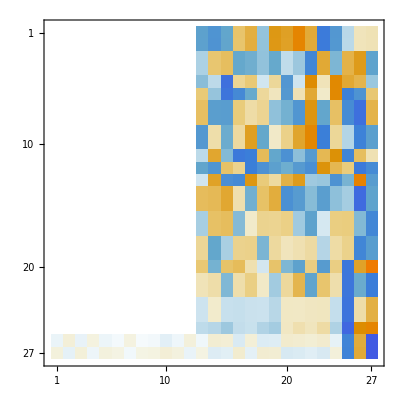

{ComplexInfinity,ComplexInfinity,-0.146844-5.33786 ⅈ,-0.146844+5.33786 ⅈ,-3.83599+0. ⅈ,2.75087+0. ⅈ,-1.13095-2.30659 ⅈ,-1.13095+2.30659 ⅈ,-2.0191+0.224868 ⅈ,-2.0191-0.224868 ⅈ,1.72635+0. ⅈ,1.29504+0. ⅈ,0.805966+0. ⅈ,-0.418531-0.0842568 ⅈ,-0.418531+0.0842568 ⅈ,-0.323511+0.229454 ⅈ,-0.323511-0.229454 ⅈ,0.204316+0.196461 ⅈ,0.204316-0.196461 ⅈ,0.256525+0. ⅈ,0.159302+0.0313006 ⅈ,0.159302-0.0313006 ⅈ,-0.08791-0.0271893 ⅈ,-0.08791+0.0271893 ⅈ,-0.0665248+0. ⅈ,2.3765×10^-8+0. ⅈ,-2.3765×10^-8+0. ⅈ}

```mathematica
MatrixPlot[NewV=Chop[Eigenvectors[{M0Big,M1Big}]]]
vv=NewV⟦-1⟧;
p1=vv⟦1;;m⟧;
Eigenvalues[{M0Big,M1Big}]
```

```mathematica
pMinGEV=-Sign[g.y2] Δ y1/(√(y1.B.y1));
f[p_]:= 0.5 p.A.p + g.p
ECons[p_]:=p.B.p-Δ^2
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
vars=Array[x,m];
vars0=RandomReal[{-1,1},m];
{FMVal,FMinSub}=FindMinimum[{0.5 vars.A.vars + g.vars,vars.B.vars<=Δ^2},{vars, vars0}ᵀ,PrecisionGoal->10] ;
pMinFM=vars/.FMinSub;
TableForm[{{FullForm[f[p]],ECons[p],G.p}/.p->pMinGEV,
{FullForm[f[p]],ECons[p]}/.p->pMinFM},
TableHeadings->{{"GEV","FindMin"},{"obj","cons: p.B.p-Δ^2"}}]
```

| obj | cons: p.B.p-Δ^2 | 
GEV | -0.00377929 | -6.93889×10^-18 | -0.0704259
0.0940681
0.147426
FindMin | -0.281915 | 9.99791×10^-9 |

```mathematica
?Partition
```